```mathematica
a=2;
f[x_]=1-a*x^2;
f[0]=0.4;
```

```mathematica
f[1]
```

-1

```mathematica
f[0]
```

0.4

```mathematica
t1=Table[y[n+1]=N[f[y[n]]],{n,0,nmax}]
nmax=100;
y[0]=f[0];
```

{0.68,0.0752,0.98869,-0.955016,-0.824109,-0.358312,0.743225,-0.104766,0.978048,-0.913156,-0.667709,0.10833,0.976529,-0.907219,-0.646092,0.165129,0.945465,-0.787807,-0.241279,0.883569,-0.561389,0.369685,0.726667,-0.0560889,0.993708,-0.974911,-0.900905,-0.623259,0.223097,0.900456,-0.621641,0.227126,0.896828,-0.6086,0.259212,0.865619,-0.498591,0.502813,0.494357,0.511222,0.477304,0.544361,0.407342,0.668145,0.107165,0.977032,-0.909181,-0.653221,0.146605,0.957014,-0.831751,-0.383618,0.705674,0.0040474,0.999967,-0.999869,-0.999476,-0.997904,-0.991624,-0.966638,-0.868777,-0.509548,0.480721,0.537814,0.421511,0.644657,0.168836,0.942989,-0.778456,-0.211987,0.910123,-0.656647,0.137628,0.962117,-0.851338,-0.449553,0.595804,0.290036,0.831758,-0.383642,0.705637,0.00415309,0.999966,-0.999862,-0.999448,-0.997793,-0.991182,-0.964883,-0.861999,-0.486083,0.527446,0.443601,0.606436,0.264471,0.86011,-0.479578,0.54001,0.416778,0.652593,0.148246,0.956046}

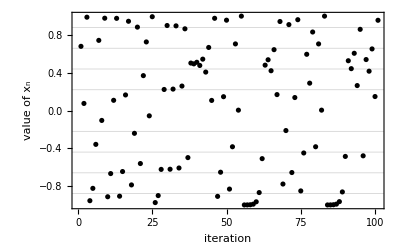

```mathematica
ListPlot[t1, PlotRange -> All, Frame -> True, GridLines->{{},{-.88, -.66, -.44, -.22, .22, .44, .66, .88}}, FrameLabel->{"iteration", Subscript [x,n] "value of"}, PlotStyle -> Black]
```

```mathematica
b1=BinCounts[t1, {{-1.1, -.88, -.66, -.44, -.22, 0, .22, .44, .66, .88, 1.1}}]
```

{16,8,12,4,3,10,9,14,9,16}

```mathematica
a1={{-.99, 16},{-.77, 8},{-.55, 12},{-.33, 4},{-.11, 3},{.11, 10},{.33, 9},{.55, 14},{.77, 9},{.99, 16}}
```

{{-0.99,16},{-0.77,8},{-0.55,12},{-0.33,4},{-0.11,3},{0.11,10},{0.33,9},{0.55,14},{0.77,9},{0.99,16}}

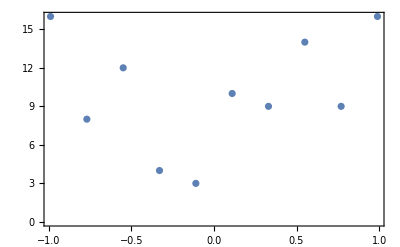

```mathematica
ListPlot[a1, PlotRange -> All, Frame -> True]
```

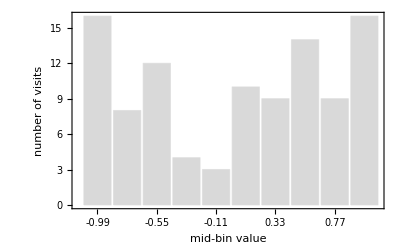

```mathematica
BarChart[{b1}, Frame -> True, ChartLabels-> Range[-.99, .99, .22], FrameLabel -> {mid-bin value, number of visits}, ChartStyle -> LightGray]
```